## Communication Complexity Bounds using Extended IC Principle

In this notebook, we provide the Mathematica code for computing lower bounds for one-way communication complexity using the extended IC principle. The notebook contains two versions: 
	1. Analytic Version (ICTerm) - computes the lower bounds in full generality but is too slow in practice
	2. Numeric Version (NumericICTerm) - computes numerical lower bounds under some weak assumptions and is much faster

For a given choice of function f(x,y), both versions compute the following quantity: I(g;f(x,y)|y=j,F_j)
The current implementation is only feasible for n <= 4. Please refer to the Python version in the repository which implements the numeric version in a much more efficient manner.

#### Analytical Version

```mathematica
ICTerm[n_,jj_]:=Module[{nx, ny,values,del,v,f, PRegister, PfFjCy, PFjCy, PfCFjy,PgCfxy,PgfFjCxy,PgfFjCy,PgFjCy,PgCyFj,PgCfFjy,PgfCy,PgCy,PgCfy},

(* 
This module analytically computes an individual term I(g;f(x,y)|y=j,Subscript[F, j]) in the extended IC statement for a given value of 'n' and 'j'. 
The guessing probability is specified as P(g=k|f(x,y)=l,x=i,y=j):=(1+(-1)^(k+l)Subscript[ϵ, ij]^l)/2 and a specific choice of the biases {Subscript[ϵ, ij]^l} is left to the user. 
*)

(* 
OPTIMISATION NOTES
 -> all functions are defined as "f[x_]:=f[x]=body" for memoization, so that the function remembers its previously computed values
-> Px[i_]:=1/nx is hardcoded so that the exponential is not computed everytime (could be changed to accomodate non-uniform distributions later)
*)

(* Parameters *)
nx=2^n;
ny=2^n;

(* Auxiliary variables to sum over the register values *)
values=Table[v[q],{q,0,jj-1}];

(* the function definition can be specified in decimal or binary form, whichever is more convenient *)
f[x_,y_]:=f[x,y]=Module[{xbit,ybit},
xbit=IntegerDigits[x,2,n];
ybit=IntegerDigits[y,2,n];

(* We give a few examples of the most commonly used functios below, please uncomment them out to use them  *)

Mod[xbit.ybit,2]                                                 (* INNER PRODUCT *)
(* Mod[∏_(k=1)^n (1+xbit[[k]]ybit[[k]]),2] *)      (* INTERSECT *)
(* If[xbit.ybit >= k, 1 ,0] *)                    (* k-INTERSECT *)
(* If[x == y, 1 ,0]*)                                        (* EQUALITY *)
(* If[x >= y, 1, 0]*)                                         (* GREATER-THAN *)
];

(* 
Here we define the necessary probability distributions and compute the mutual information from the joint distribution of the guess and the function values. 

The notation for the conditional probalitlity distribution functions defined below is as follows: P( Subscript[var, 1]=Subscript[v, 1],..., Subscript[var, n]=Subscript[v, n] | Subscript[cond, 1]=Subscript[x, 1],...,Subscript[cond, n]=Subscript[x, n])= Pvar1...varnCcond1...condn[v1,...,vn][x1,...,xn]
so as an example P(g=k,f(x,y)=l,Subscript[F, j]={values}|x=i,y=j)-> PgfFjCxy[k, l, values][i, j]

We also introduce a regulator variable 'del' so that logarithms and denominators behave properly. This is set to zero at the very last step.
*)

(* Type 1 Distributions (these distributions are related to the register and structure of the function) *)
PRegister[l_,values_][i_,j_]:=PRegister[l,values][i,j]=KroneckerDelta[f[i,j],l]If[j==0,1,∏_(k=0)^(j-1) KroneckerDelta[f[i,k],values[[k+1]]]];
PfFjCy[l_,values_][j_]:=PfFjCy[l,values][j]=1/nx∑_(i=0)^(nx-1) PRegister[l,values][i,j];
PFjCy[values_][j_]:=PFjCy[values][j]=1/nx∑_(l=0)^1 ∑_(i=0)^(nx-1) PRegister[l,values][i,j];
PfCFjy[l_][values_,j_]:=PfCFjy[l][values,j]=(PfFjCy[l,values][j])/(PFjCy[values][j]+del);

(* Type 2 Distributions (these distributions are related to the guessing probability and the protocol) *)

PgCfxy[k_][l_,i_,j_]:=PgCfxy[k][l,i,j]=(1+(-1)^(k+l)ϵ[l,i,j])/2;
PgfFjCxy[k_,l_,values_][i_,j_]:=PgfFjCxy[k,l,values][i,j]=PgCfxy[k][l,i,j]PRegister[l,values][i,j];
PgfFjCy[k_,l_,values_][j_]:=PgfFjCy[k,l,values][j]=1/nx∑_(i=0)^(nx-1) PgCfxy[k][l,i,j]PRegister[l,values][i,j];
PgFjCy[k_,values_][j_]:=PgFjCy[k,values][j]=1/nx∑_(i=0)^(nx-1) ∑_(l=0)^1 PgCfxy[k][l,i,j]PRegister[l,values][i,j];

PgCyFj[k_][j_,values_]:=PgCyFj[k][j,values]=(PgFjCy[k,values][j])/(PFjCy[values][j]+del);

PgCfFjy[k_][l_,values_,j_]:=PgCfFjy[k][l,values,j]=(PgfFjCy[k,l,values][j])/(PfFjCy[l,values][j]+del);

(* these distributions are only relevant when j=0, since the register Subscript[F, j] is empty for j=0 *)
PgfCy[k_,l_]:=1/nx∑_(i=0)^(nx-1) PgCfxy[k][l,i,jj] KroneckerDelta[ f[i,jj],l];
PgCy[k_]:=∑_(l=0)^1 PgfCy[k,l];
PgCfy[k_][l_]:=PgfCy[k,l]/(1/nx∑_(i=0)^(nx-1) KroneckerDelta[ f[i,jj],l]+del);

(* Here we compute the individual mutual information term I(g;f(x,y)|y=j, Subscript[F, j]) by breaking it into 2 parts as I(g;f(x,y)|y=j, Subscript[F, j])=H(g|y=j, Subscript[F, j])-H(g|y=j, Subscript[F, j],f(x,y)) *)

If[jj==0,
(-∑_(k=0)^1 PgCy[k]Log[2,PgCy[k]+del]+∑_(k=0)^1 ∑_(l=0)^1 PgfCy[k,l]Log[2,PgCfy[k][l]+del])/.{del->0}//Simplify
,Sum[PFjCy[values][jj]((-∑_(k=0)^1 PgCyFj[k][jj,values]Log[2,PgCyFj[k][jj,values]+del])-∑_(ll=0)^1 (PfCFjy[ll][values,jj](-∑_(k=0)^1 PgCfFjy[k][ll,values,jj]Log[2,PgCfFjy[k][ll,values,jj]+del]))),Evaluate[Sequence @@Table[{v[i],0,1},{i,0,jj-1}]]]/.{del->0}//Simplify]]
```

#### Numerical Version

```mathematica
NumericICTerm[n_,jj_]:=Module[{nx, ny,values,del,v,ϵ,f, RegValues,PRegister, PfFjCy, PFjCy, PfCFjy,PgCfxy,PgfFjCxy,PgfFjCy,PgFjCy,PgCyFj,PgCfFjy,PgfCy,PgCy,PgCfy},

(* 
This module numerically computes an individual term I(g;f(x,y)|y=j,Subscript[F, j]) in the extended IC statement for a given value of 'n' and 'j'. 
The guessing probability is specified as P(g=k|f(x,y)=l,x=i,y=j):=(1+(-1)^(k+l)ϵ)/2 and thus is independent of x,y and the function's value.
*)

(* 
OPTIMISATION NOTES
 -> functions are defined as "f[x_]:=f[x]=body" for memoization,so that the function remembers its previously computed values
-> Px[i_]:=1/nx is hardcoded so that the exponential is not computed everytime (this could be changed to accomodate non-uniform distributions later)
-> distributions are rewritten in terms of motifs which keep appearing in the joint distributions
-> the expression for the entropy is compiled where the joint distribution for the guess reduces to the bare distribution

*)

(* Parameters *)
nx=2^n;
ny=2^n;

(* Auxiliary variables to sum over the register values *)
values=Table[v[q],{q,0,jj-1}];

(* the function definition can be specified in decimal or binary form, whichever is more convenient *)
f[x_,y_]:=f[x,y]=Module[{xbit,ybit},
xbit=IntegerDigits[x,2,n];
ybit=IntegerDigits[y,2,n];

(* We give a few examples of the most commonly used functios below, please uncomment them out to use them  *)

Mod[xbit.ybit,2]                                                 (* INNER PRODUCT *)
(* Mod[∏_(k=1)^n (1+xbit[[k]]ybit[[k]]),2] *)      (* INTERSECT *)
(* If[xbit.ybit >= k, 1 ,0] *)                    (* k-INTERSECT *)
(* If[x == y, 1 ,0]*)                                        (* EQUALITY *)
(* If[x >= y, 1, 0]*)                                         (* GREATER-THAN *)
];

(* 
Here we define the necessary probability distributions and compute the mutual information from the joint distribution of the guess and the function values. 
The notation for the conditional probalitlity distribution functions defined below is as follows: P( Subscript[var, 1]=Subscript[v, 1],..., Subscript[var, n]=Subscript[v, n] | Subscript[cond, 1]=Subscript[x, 1],...,Subscript[cond, n]=Subscript[x, n])= Pvar1...varnCcond1...condn[v1,...,vn][x1,...,xn]
so as an example P(g=k,f(x,y)=l,Subscript[F, j]={values}|x=i,y=j)-> PgfFjCxy[k, l, values][i, j]
*)

(* Type 1 Distributions (these distributions are related to the register and structure of the function) *)
RegValues[regval_][i_,j_]:=RegValues[regval][i,j]=∏_(k=0)^(j-1) KroneckerDelta[f[i,k],regval[[k+1]]];
PFjCy[values_][j_]:=PFjCy[values][j]=1/nx Sum[RegValues[values][i,j],{i,0,nx-1}];
PfCFjy[l_][values_,j_]:=PfCFjy[l][values,j]=Sum[KroneckerDelta[f[i,j],l]RegValues[values][i,j],{i,0,nx-1}]/(nx PFjCy[values][j]+del);

(* Type 2 Distributions (these distributions are related to the guessing probability and the protocol) *)

PgCfxy[k_][l_]:=PgCfxy[k][l]=(1+(-1)^(k+l)ϵ)/2;

PgCyFj[k_][j_,values_]:=PgCyFj[k][j,values]=Sum[PgCfxy[k][f[i,j]]RegValues[values][i,j],{i,0,nx-1}]/(nx PFjCy[values][j]+del);

(* these distributions are only relevant when j=0, since the register Subscript[F, j] is empty for j=0 *)
PgfCy[k_,l_]:=1/nx∑_(i=0)^(nx-1) PgCfxy[k][l]KroneckerDelta[f[i,0],l];
PgCy[k_]:=1/nx∑_(i=0)^(nx-1) PgCfxy[k][f[i,0]];
PgCfy[k_][l_]:=PgCfxy[k][l];

(* Here we compute the individual mutual information term I(g;f(x,y)|y=j, Subscript[F, j]) by breaking it into 2 parts as I(g;f(x,y)|y=j, Subscript[F, j])=H(g|y=j, Subscript[F, j])-H(g|y=j, Subscript[F, j],f(x,y)). 

In the very last step we set the value for ϵ (default=0.7) and invoke the '//N' method to compute these expressions nuemrically. This winning bias can be easily changed to 1 for computing deterministic bounds or scaled accordingly to see the behaviour of randomised complexity bounds w.r.t success probability.

We also introduce a regulator variable 'del' so that logarithms and denominators behave properly. This is set to zero at the very last step.
*)

If[jj==0,
(-∑_(k=0)^1 PgCy[k]Log[2,PgCy[k]+del]+∑_(k=0)^1 ∑_(l=0)^1 PgfCy[k,l]Log[2,PgCfy[k][l]+del])/.{del->0}/.{ϵ->0.7}//N//Simplify
,Sum[PFjCy[values][jj]((-∑_(k=0)^1 PgCyFj[k][jj,values]Log[2,PgCyFj[k][jj,values]+del])-∑_(ll=0)^1 (PfCFjy[ll][values,jj](-∑_(k=0)^1 PgCfxy[k][ll]Log[2,PgCfxy[k][ll]+del]))),Evaluate[Sequence @@Table[{v[i],0,1},{i,0,jj-1}]]]/.{del->0}/.{ϵ->0.7}//N//Simplify]]
```

### Examples

We illustrate the use by considering the inner product function. As a warm up, we compute all the terms for n=3. Here we will assume that the winning probability is independent of the inputs (as is standard in the definition of randomised communication complexity where a protocol succeeds with probability greater than 1/2 for all inputs x,y) and thus ϵ_ij^l->ϵ.

```mathematica
Terms=Table[{ICTerm[3,j],j},{j,0,8}]/.{ϵ[l_,i_,j_]->ϵ}//Simplify;
Terms//MatrixForm
```

(0 | 0
(-((-1+ϵ) Log[1-ϵ])+(1+ϵ) Log[1+ϵ])/Log[4] | 1
(-((-1+ϵ) Log[1-ϵ])+(1+ϵ) Log[1+ϵ])/Log[4] | 2
0 | 3
(-((-1+ϵ) Log[1-ϵ])+(1+ϵ) Log[1+ϵ])/Log[4] | 4
0 | 5
0 | 6
0 | 7
0 | 8)

We repeat the same using the numeric version as well below.

```mathematica
Terms=Table[{NumericICTerm[3,j],j},{j,0,8}];
Terms//MatrixForm
```

(0. | 0
0.39016 | 1
0.39016 | 2
0. | 3
0.39016 | 4
0. | 5
0. | 6
0. | 7
0. | 8)

We notice that all the terms for which j!=2^n vanish. To compute the lower bound, we simply sum this table. In general we can define the total IC function as follows

```mathematica
TotalIC[n_]:=Sum[NumericICTerm[n,j],{j,0,2^n-1}]
```

{{1,0.39016},{2,0.780319},{3,1.17048},{4,1.56064}}

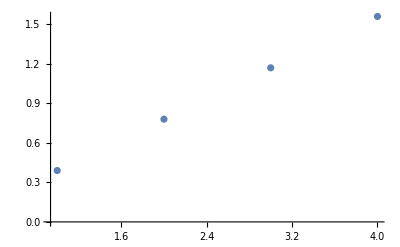

FittedModel[6.99441×10^-16+0.39016 x]

```mathematica
LowerBounds=Table[{n,TotalIC[n]},{n,1,4}]
ListPlot[LowerBounds]
ScalingFit=LinearModelFit[LowerBounds,x,x]
```

We see that the fit is linear and hence the communication complexity of the inner product function scales as Ω(n). Arguably, n=4 is too small to conclude anything for the asymptotic behavior of the function but this notebook intends to serve as a proof of concept rather than as an efficient tool for computing lower bounds.